```mathematica
Integrate[1-1/(d+H^(3/2) (1-d)), x]
```

x-x/(d+(1-d) H^(3/2))

```mathematica
Integrate[(d+h^(3/2) (1-d))/(d+h^(3/2) (1-d)-1), h]
```

(-3 h+3 d h-2 √3 ArcTan[(1+2 √h)/(√3)]-2 Log[-1+√h]+Log[1+√h+h])/(-3+3 d)

```mathematica
Integrate[(h^n(-1+β +h/fr^2))/(h^(n+1)-1), h]
```

1/(fr^2 (1+n))(h+h n-h (1+n) Hypergeometric2F1[1,1/(1+n),1+1/(1+n),h^(1+n)]+fr^2 (1+n) (-1+β) Log[h]+fr^2 Log[h^(1+n)/(1-h^(1+n))]-fr^2 β Log[h^(1+n)/(1-h^(1+n))])

```mathematica
Assuming[{n∈ PositiveReals && fr∈ PositiveReals&& β∈ PositiveReals && β>=1 }, Integrate[(h^n(-1+β +h/fr^2))/(h^(n+1)-1), h]]
```

1/(fr^2 (1+n))(h+h n-h (1+n) Hypergeometric2F1[1,1/(1+n),1+1/(1+n),h^(1+n)]+fr^2 (1+n) (-1+β) Log[h]+fr^2 Log[h^(1+n)/(1-h^(1+n))]-fr^2 β Log[h^(1+n)/(1-h^(1+n))])

```mathematica
depthProfile[h_, fr_, n_, β_]:=1/(fr^2 (1+n))(h+h n-h (1+n) Hypergeometric2F1[1,1/(1+n),1+1/(1+n),h^(1+n)]+fr^2 (1+n) (-1+β) Log[h]+fr^2 Log[h^(1+n)/(1-h^(1+n))]-fr^2 β Log[h^(1+n)/(1-h^(1+n))])
```

```mathematica
depthProfile[0.90, 1.20, 0.30, 1.103448]
```

-0.866385

```mathematica
depthProfile[0.0001, 1.20, 0.30, 1.103448]
```

-5.02279×10^-7

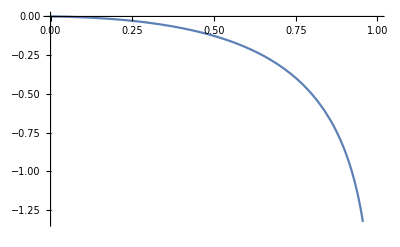

```mathematica
Plot[depthProfile[h, 1.20, 0.30, 1.103448], {h, 0.00001, 0.9999}]
```

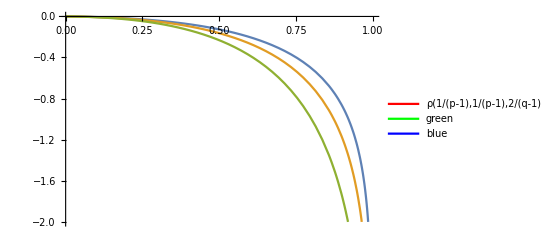

```mathematica
Plot[{depthProfile[h, 1.20, 0.30, 1.103448], depthProfile[h, 1.00, 0.30, 1.103448], depthProfile[h, 0.80, 0.30, 1.103448]}, {h, 0.00001, 0.99999}, PlotLegends->LineLegend[{Red,Green,Blue},{Text[Style[ToExpression["\\rho\\left({{1/(p-1),1/(p-1)},{2/(q-1),0}}\\right)=1",TeXForm,HoldForm],Bold]],"green","blue"} ,LabelStyle->{FontFamily->"Times New Roman",FontSize->24, FontSlant->Italic,FontWeight->"Heavy"}]]
```

```mathematica
Needs["MaTeX`"]
```

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
MaTeX[HoldForm@Integrate[Exp[-x],{x,0,Infinity}]]
```

-Graphics-

```mathematica
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.01.2\\bin\\gswin64c.exe"]
```

{pdfLaTeX→C:\Users\byy\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:\Program Files\gs\gs10.01.2\bin\gswin64c.exe}

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k^2} = \\frac{\\pi^2}{6}",FontSize->24]
```

-Graphics-

```mathematica
pl=HoldForm[p {{a,b},{c,d}}==1];
plt=MaTeX[TeXForm@pl,Magnification->1.5];
```

```mathematica
plt
```

-Graphics-

```mathematica
lg1 = MaTeX["\\text{Fr}=1.20", FontSize->18];
lg2= MaTeX["\\text{Fr}=1.00", FontSize->18];
lg3 = MaTeX["\\text{Fr}=0.80", FontSize->18];
```

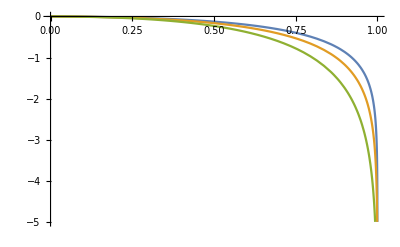

```mathematica
Plot[{depthProfile[h, 1.20, 0.30, 1.103448], depthProfile[h, 1.00, 0.30, 1.103448], depthProfile[h, 0.80, 0.30, 1.103448]}, {h, 0.000001, 0.999999}, PlotRange->{-5,0}, PlotLegends->LineLegend[ {lg1,lg2,lg3} ,LabelStyle->{FontFamily->"Times New Roman",FontSize->24, FontSlant->Italic,FontWeight->"Heavy"}]]
```